# Synthesizing Sound Effects

## Yen Lee Loh, 2021-7-6

## Section Sound effects

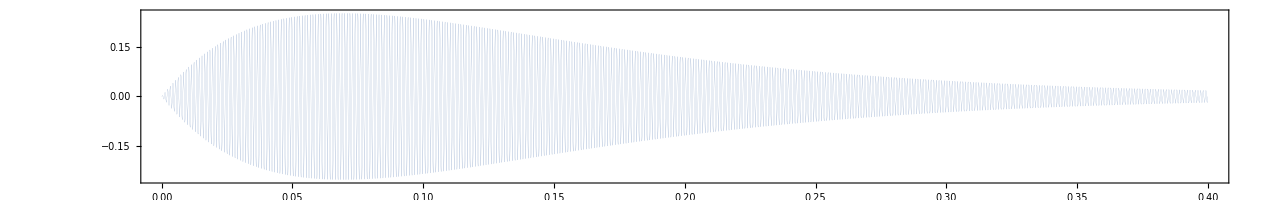

```mathematica
ding[t_,f_,tau_]:=Sin[f*2π t]*(Exp[-t/tau]-Exp[-2t/tau])*UnitStep[t];
Plot[ding[t,990,0.1],{t,0,0.4},PlotPoints->1000,ImageSize->{1280,200},AspectRatio->Full,PlotStyle->AbsoluteThickness@0]
```

```mathematica
snd=Play[
ding[t,990,0.15]
,{t,0,2},SampleRate->44100,PlayRange->All]
snd//EmitSound
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"ding.mp3",snd];
```

```mathematica
snd=Play[
0.5ding[t,990,0.15]+0.5ding[t-.1,1320,0.15]
,{t,0,2},SampleRate->44100,PlayRange->All]
snd//EmitSound
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"dingling.mp3",snd];
```

```mathematica
freq[t_]:=1000(1-t)^5;
phase[t_]=Integrate[freq[t],t]
```

-500/3 (-1+t)^6

```mathematica
snd=Play[
Sin[2π*phase[t]]
,{t,0,1},SampleRate->44100,PlayRange->All];
snd//EmitSound
```

```mathematica
Export[NotebookDirectory[]<>"fall.mp3",snd];
```

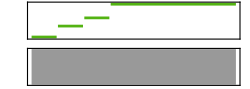

```mathematica
inst="Harp";
snd=Sound[{SoundNote["C5",.1,inst],SoundNote["E5",.1,inst],SoundNote["G5",.1,inst],SoundNote["C6",.5,inst]}]
snd//EmitSound
```

```mathematica
Export[NotebookDirectory[]<>"win.mp3",snd];
```

## Section Aiming a camera to capture a scene

Consider a game board centered at (0,0,0) and extending from -w/2<x<w/2 to -h/2<y<h/2.
We have a camera whose bottom-to-top angular field of view is 2θ.  The center of the camera’s view is aimed at angle α (but the centerline does not necessarily pass through the origin).  A simple geometrical construction shows that the angles of the bottom and top of the camera’s view α_B and α_T satisfy
	α_B=α+θ
	α_T=α-θ.
Let the camera position be (0,-Y,Z).  We wish to aim a camera such that the bottom and the top of the board are just captured.  This means that
	α+θ=arctan Z/(Y-h/2),
	α-θ=arctan Z/(Y+h/2).

We know h, θ, α.  We wish find Y and Z.  Eliminating Z gives (α+θ)tan (α+θ)=(Y+h/2)tan (α-θ).  Rearranging for Y gives
	Y=h/2(tan (α+θ)+tan(α-θ))/(tan (α+θ)-tan (α-θ))=h/2(sin 2α)/(sin 2θ).
Then
	Z=(Y-h/2)tan(α+θ)=h/2((tan (θ+α)+tan(θ-α))/(tan (θ+α)-tan (θ-α))-1)tan(α+θ).
The camera distance from the origin is d=√(Y^2+Z^2), i.e.,
	d=h/2(√(3+Cos[4 α]-4 Cos[2 α] Cos[2 θ]) Csc[2 α])/(√2).
The inclination of the line from the camera to the origin is 
	α_true=arctan Z/Y.

```mathematica
Clear[θ,α];
(Tan[α+θ]+Tan[α-θ])/(Tan[α+θ]-Tan[α-θ])//FullSimplify
Sin[2α]/Sin[2θ]//FullSimplify
((Tan[α+θ]+Tan[α-θ])/(Tan[α+θ]-Tan[α-θ])-1)Tan[θ+α]//FullSimplify
√(((Tan[α+θ]+Tan[α-θ])/(Tan[α+θ]-Tan[α-θ]))^2+(((Tan[α+θ]+Tan[α-θ])/(Tan[α+θ]-Tan[α-θ])-1)Tan[α+θ])^2)//FullSimplify//PowerExpand//Simplify
```

Cos[α] Csc[θ] Sec[θ] Sin[α]

Cos[α] Csc[θ] Sec[θ] Sin[α]

Cot[2 θ]-Cos[2 α] Csc[2 θ]

√(-1+Cos[α]^2 Sec[θ]^2+Csc[θ]^2 Sin[α]^2)

We now need to check whether the left and right of the board are captured.  If the camera view were square, then the width of the board would be reduced by the camera’s aspect ratio γ, and the horizontal FoV would also be 2θ.  Based on this, the camera distance would be
	d=(w γ)/2 cot θ.
Ultimately we want to take d=max(d_1,d_2) in order to make sure the entire scene (horizontal and vertical) is captured.

#### Demo

```mathematica
0.57/Degree
```

32.6586

```mathematica
w=2.;h=1.;θ=25°;α=45°;γ=3/4;(*9/16;*)
Y=h/2 Sin[2α]/Sin[2θ];
Z=h/2(Sin[2α]/Sin[2θ]-1)Tan[α+θ];
αTrue=ArcTan[Z/Y];
d1=√(Y^2+Z^2)
d2=(w γ)/2 Cot[θ]
d=Max[d1,d2]

rr=d*{0,-Cos[αTrue],Sin[αTrue]};(* camera position *)
angleABC[a_,b_,c_]:=ArcCos[((a-b).(c-b))/(√((a-b).(a-b))√((c-b).(c-b)))];
Print["camPos = ",rr,{0,-Y,Z}]
Print["α, αTrue = ",α,"  ",αTrue/Degree*"°"]
Print["Left-right angle = ",angleABC[{-w/2,0,0},rr,{+w/2,0,0}]/Degree*"°"]
Print["Top-bottom angle = ",angleABC[{0,-h/2,0},rr,{0,+h/2,0}]/Degree*"°"]
```

0.775915

1.60838

1.60838

camPos = {0.,-1.35298,0.869677}{0,-0.652704,0.41955}

α, αTrue = 45 °  32.7324 °

Left-right angle = 63.742 °

Top-bottom angle = 20.4129 °

```mathematica
Graphics3D[{
Blue,
Cuboid[{-w/2,-h/2,-.1},{w/2,h/2,0}],
Red,
Sphere[d1*{0,-Cos[αTrue],Sin[αTrue]},.04],
Sphere[d2*{0,-Cos[αTrue],Sin[αTrue]},.04],
Tube[{rr,{0,0,0}},.02],
Opacity[.25,Red],
Tube[{rr,{w/2,0,0}},.01],
Tube[{rr,{-w/2,0,0}},.01],
Tube[{rr,{0,h/2,0}},.01],
Tube[{rr,{0,-h/2,0}},.01],
Opacity[.25,Yellow],
Cone[{{0,0,0},{0,0,d}},d*Tan[θ]]//Scale[#,{1/γ,1,1}]&//Rotate[#,{{0,0,1},{0,-Cos[αTrue],Sin[αTrue]}}]&,
Cone[{{0,0,0},{0,0,d}},d*Tan[θ]]//Scale[#,{1,γ,1}]&//Rotate[#,{{0,0,1},{0,-Cos[αTrue],Sin[αTrue]}}]&
},PlotRange->All,Axes->True,Boxed->True,ViewPoint->100{3,-1,2},ViewVertical->{0,0,1},ViewAngle->Automatic,ImageSize->400]
```

-Graphics3D-

## Section Image processing

```mathematica
a=Import[NotebookDirectory[]<>"/arrow.jpg"];
b=ImageApply[Round,a];
c=ImagePad[b,512,"Fixed"];
d=ImageResize[c,512];
Show[#,ImageSize->100]&/@{a,b,c}
Export[NotebookDirectory[]<>"/arrow2.jpg",d];
```

{-Graphics-,-Graphics-,-Graphics-}

## Section Cartesian and hexagonal coordinates

(x
y)=(1 | -1/2
0 | √3/2)(u
v)
	(u
v)=(1 | 1/√3
0 | 2/√3)(x
y)

```mathematica
Inverse[({{1, -1/2}, {0, √3/2}})]
```

```mathematica
{{1,1/(√3)},{0,2/(√3)}}//N
```

```mathematica
{{1.,0.5773502691896258},{0.,1.1547005383792517}}
```

## Initialization cells (best version as of 2021-5-26)

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={};myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black},ImageMargins->1};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS];
SetOptions[ListLinePlot,myGS,myPS];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[DiscretePlot,myGS,myPS];
SetOptions[RectangleChart,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicks$TickColor=Black; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myRealPlot and myComplexPlot

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```